## Polynomial Model

(5 | 5 | 10 | 10 | 15 | 15 | 20 | 20 | 25 | 25
14 | 12.5 | 7 | 5 | 2.1 | 1.8 | 6.2 | 4.9 | 13.2 | 14.6)

{10,2}

(27.3
-3.313
0.111)

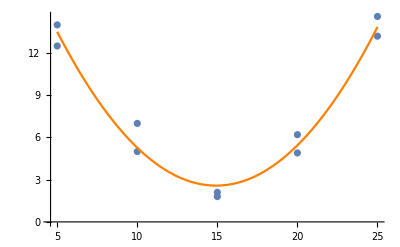

27.3-3.313 u+0.111 u^2

```mathematica
data = {{5,14},{5,12.5},{10,7},{10,5},{15,2.1},{15,1.8},{20,6.2},{20,4.9},{25,13.2},{25,14.6}};
MatrixForm[Transpose[data]]
p = 2;
n=Dimensions[data][[1]];{n,p}
y= Transpose[data][[2]];
X = Transpose[Table[Function[x,x^k] /@Transpose[data][[1]],{k,0,p}]];
{MatrixForm[X], MatrixForm[y]};
b = Inverse[Transpose[X].X].Transpose[X].y;
MatrixForm[b]
P0=ListPlot[data];
P1 = Plot[Sum[b[[i+1]]*x^i,{i,0,p}],{x,5,25}, PlotStyle->Orange];
Show[P0,P1]
model = NonlinearModelFit[data, b0+b1*u + b2*u^2,{b0,b1,b2},u];
model["BestFit"]
```

## Multilinear Model

```mathematica
(*x1,x2,y*)rowdata:= {{1.35,1.90,1.70,1.80,1.30,2.05,1.60,1.80,1.85,1.40},{90,30,80,40,35,45,50,60,65,30},{17.9,16.5,16.4,16.8,18.8,15.5,17.5,16.4,15.9,18.3}};
MatrixForm[rowdata]
{n,p} = Dimensions[Transpose[rowdata]] ;p=p-1;
{n,p}
X = Transpose[Join[{Table[1,{i,1,n}]},rowdata[[1;;p]]]];
y = rowdata[[p+1]];
{MatrixForm[X], MatrixForm[y]};
(*Multilinear Regression b*)
b = Inverse[Transpose[X].X].Transpose[X].y; 
MatrixForm[b]
SSR = b.(Transpose[X].y)-1/n*(Total[y])^2;
SST = Sum[y[[i]]^2, {i,1,n}]-1/n*(Total[y])^2;
SSE = SST-SSR;
(*R^2, s^2*)
R2 = SSR/SST;
s2 = SSE/(n-p-1);
{R2,s2}
(*Significance of Regression {F statics, alpha=0.05 threshold, P value}*)
F = (n-p-1)/p*R2/(1-R2);
{F,InverseCDF[FRatioDistribution[p,n-p-1],0.95],(1-CDF[FRatioDistribution[p,n-p-1],F])}
(*Var[b]*)
MatrixForm[s2*Inverse[Transpose[X].X]]
P0 = ListPointPlot3D[Transpose[rowdata]];
P1 = Plot3D[b[[1]]+b[[2]]*x1+b[[3]]*x2,{x1,1.3,2.1},{x2,20,90}, PlotStyle->Directive[Opacity[0.7],Orange]];
Show[P1,P0]

(*Predicti Y|x*)
MatrixForm[x0 = {1,1.5,70}];
muY = b.x0;
errorY = InverseCDF[StudentTDistribution[n-p-1], 1-0.025]*Sqrt[s2]*Sqrt[1+x0.Inverse[Transpose[X].X].x0];
{muY-errorY, muY+errorY}

(*predict muY|x*)
errorMuY =  InverseCDF[StudentTDistribution[n-p-1], 1-0.025]*Sqrt[s2]*Sqrt[x0.Inverse[Transpose[X].X].x0];
{muY-errorMuY, muY+errorMuY}
```

(1.35 | 1.9 | 1.7 | 1.8 | 1.3 | 2.05 | 1.6 | 1.8 | 1.85 | 1.4
90 | 30 | 80 | 40 | 35 | 45 | 50 | 60 | 65 | 30
17.9 | 16.5 | 16.4 | 16.8 | 18.8 | 15.5 | 17.5 | 16.4 | 15.9 | 18.3)

{10,2}

(24.7489
-4.15933
-0.014895)

{0.986582,0.02005}

{257.348,4.73741,2.79821×10^-7}

(0.121719 | -0.0606689 | -0.000344635
-0.0606689 | 0.0348589 | 0.0000434344
-0.000344635 | 0.0000434344 | 5.17871×10^-6)

-Graphics3D-

{17.0975,17.8369}

{17.3105,17.6239}

```mathematica
(*model method*)
model = LinearModelFit[{X,y}];
Evaluate[model["BestFit"]]&[1,x1,x2]
model["EstimatedVariance"] 
model["RSquared"]
MatrixForm[model["CovarianceMatrix"]]
model["ParameterConfidenceIntervalTable"]
model["MeanPredictionBands"] /. {x1-> 1.5, x2-> 70}
```

24.7489-4.15933 x1-0.014895 x2

0.02005

0.986582

(0.121719 | -0.0606689 | -0.000344635
-0.0606689 | 0.0348589 | 0.0000434344
-0.000344635 | 0.0000434344 | 5.17871×10^-6)

| Estimate | Standard Error | Confidence Interval
#1 | 24.7489 | 0.348882 | {23.9239,25.5738}
#2 | -4.15933 | 0.186705 | {-4.60082,-3.71785}
#3 | -0.014895 | 0.00227568 | {-0.0202761,-0.00951389}

{24.7489 #1-4.15933 #2-0.014895 #3-2.36462 √(0.121719 #1^2-0.121338 #1 #2+0.0348589 #2^2-0.00068927 #1 #3+0.0000868687 #2 #3+5.17871×10^-6 #3^2),24.7489 #1-4.15933 #2-0.014895 #3+2.36462 √(0.121719 #1^2-0.121338 #1 #2+0.0348589 #2^2-0.00068927 #1 #3+0.0000868687 #2 #3+5.17871×10^-6 #3^2)}